```mathematica
g1=FindFullFormula[Graph[GraphFromSets[{{1,3},{2,6},{4,7},{5}}]]]
```

{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x26x3x4x5x7,v1x26x3x47x5,v13x2x4x5x6x7,v13x2x47x5x6,v13x26x4x5x7,v13x26x47x5}

```mathematica
g2=FindFullFormula[Graph[GraphFromSets[{{1,6},{2,4},{3,7},{5}}]]]
```

{v1x2x3x4x5x6x7,v1x2x37x4x5x6,v1x24x3x5x6x7,v1x24x37x5x6,v16x2x3x4x5x7,v16x2x37x4x5,v16x24x3x5x7,v16x24x37x5}

```mathematica
g3=FindFullFormula[Graph[GraphFromSets[{{1,6},{2,7},{3,5},{4}}]]]
```

{v1x2x3x4x5x6x7,v1x2x35x4x6x7,v1x27x3x4x5x6,v1x27x35x4x6,v16x2x3x4x5x7,v16x2x35x4x7,v16x27x3x4x5,v16x27x35x4}

```mathematica
g4=FindFullFormula[Graph[GraphFromSets[{{1,4},{2,6},{3,7},{5}}]]]
```

{v1x2x3x4x5x6x7,v1x2x37x4x5x6,v1x26x3x4x5x7,v1x26x37x4x5,v14x2x3x5x6x7,v14x2x37x5x6,v14x26x3x5x7,v14x26x37x5}

```mathematica
g5=FindFullFormula[Graph[GraphFromSets[{{1,6},{2,5},{3,7},{4}}]]]
```

{v1x2x3x4x5x6x7,v1x2x37x4x5x6,v1x25x3x4x6x7,v1x25x37x4x6,v16x2x3x4x5x7,v16x2x37x4x5,v16x25x3x4x7,v16x25x37x4}

```mathematica
Tally[Join[g1,g2,g3,g4,g5]]
```

{{v1x2x3x4x5x6x7,5},{v1x2x3x47x5x6,1},{v1x26x3x4x5x7,2},{v1x26x3x47x5,1},{v13x2x4x5x6x7,1},{v13x2x47x5x6,1},{v13x26x4x5x7,1},{v13x26x47x5,1},{v1x2x37x4x5x6,3},{v1x24x3x5x6x7,1},{v1x24x37x5x6,1},{v16x2x3x4x5x7,3},{v16x2x37x4x5,2},{v16x24x3x5x7,1},{v16x24x37x5,1},{v1x2x35x4x6x7,1},{v1x27x3x4x5x6,1},{v1x27x35x4x6,1},{v16x2x35x4x7,1},{v16x27x3x4x5,1},{v16x27x35x4,1},{v1x26x37x4x5,1},{v14x2x3x5x6x7,1},{v14x2x37x5x6,1},{v14x26x3x5x7,1},{v14x26x37x5,1},{v1x25x3x4x6x7,1},{v1x25x37x4x6,1},{v16x25x3x4x7,1},{v16x25x37x4,1}}

```mathematica
gall=With[{
part1={{1,3},{2,6},{4,7},{5}},
part2={{1,6},{2,4},{3,7},{5}},
part3={{1,6},{2,7},{3,5},{4}},
part4={{1,4},{2,6},{3,7},{5}},
part5={{1,6},{2,5},{3,7},{4}}},
With[{g=EdgeDelete[
CompleteGraph[7],
DeleteDuplicates[
Join[
EdgeList[GraphComplement[GraphFromSets[part1]]],
EdgeList[GraphComplement[GraphFromSets[part2]]],
EdgeList[GraphComplement[GraphFromSets[part3]]],
EdgeList[GraphComplement[GraphFromSets[part4]]],
EdgeList[GraphComplement[GraphFromSets[part5]]]
]
]
]},
FindFullFormula[g]
]
]
```

{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x2x37x4x5x6,v1x2x35x4x6x7,v1x2x35x47x6,v1x27x3x4x5x6,v1x27x35x4x6,v1x26x3x4x5x7,v1x26x3x47x5,v1x26x37x4x5,v1x26x35x4x7,v1x26x35x47,v1x25x3x4x6x7,v1x25x3x47x6,v1x25x37x4x6,v1x24x3x5x6x7,v1x247x3x5x6,v1x24x37x5x6,v1x24x35x6x7,v1x247x35x6,v16x2x3x4x5x7,v16x2x3x47x5,v16x2x37x4x5,v16x2x35x4x7,v16x2x35x47,v16x27x3x4x5,v16x27x35x4,v16x25x3x4x7,v16x25x3x47,v16x25x37x4,v16x24x3x5x7,v16x247x3x5,v16x24x37x5,v16x24x35x7,v16x247x35,v14x2x3x5x6x7,v14x2x37x5x6,v14x2x35x6x7,v14x27x3x5x6,v14x27x35x6,v14x26x3x5x7,v14x26x37x5,v14x26x35x7,v14x25x3x6x7,v14x25x37x6,v13x2x4x5x6x7,v13x2x47x5x6,v13x27x4x5x6,v13x26x4x5x7,v13x26x47x5,v13x25x4x6x7,v13x25x47x6,v13x24x5x6x7,v13x247x5x6}

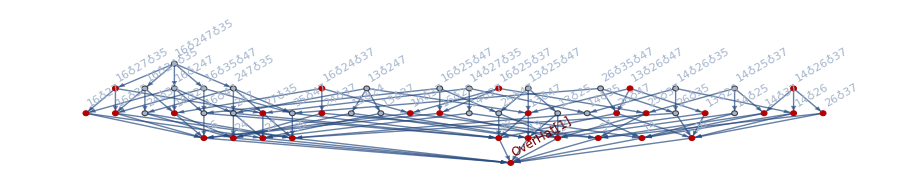

```mathematica
Graph[FormulaGraphReverse[gall],GraphHighlight->DeleteDuplicates[Join[g1,g2,g3,g4,g5]],ImageSize->800]
```

```mathematica
gall12=With[{
part1={{1,3},{2,6},{4,7},{5}},
part2={{1,6},{2,4},{3,7},{5}},
part3={{1,6},{2,7},{3,5},{4}},
part4={{1,4},{2,6},{3,7},{5}},
part5={{1,6},{2,5},{3,7},{4}}},
With[{g=EdgeDelete[
CompleteGraph[7],
DeleteDuplicates[
Join[
EdgeList[GraphComplement[GraphFromSets[part1]]],
EdgeList[GraphComplement[GraphFromSets[part2]]]
]
]
]},
FindFullFormula[g]
]
]
```

{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x2x37x4x5x6,v1x26x3x4x5x7,v1x26x3x47x5,v1x26x37x4x5,v1x24x3x5x6x7,v1x24x37x5x6,v16x2x3x4x5x7,v16x2x3x47x5,v16x2x37x4x5,v16x24x3x5x7,v16x24x37x5,v13x2x4x5x6x7,v13x2x47x5x6,v13x26x4x5x7,v13x26x47x5,v13x24x5x6x7}

```mathematica
ColorSchemeForLists[l1_,l2_]:=Block[{
int = Intersection[l1,l2]},
Join[
Table[e->Darker[Green],{e,SetDifference[l1,int]}],
Table[e->Blue,{e,SetDifference[l2,int]}],
Table[e->Red,{e,int}]
]
]
```

```mathematica
ColorSchemeForLists[g1,g3]
```

{v1x2x3x47x5x6→RGBColor[0, Rational[2, 3], 0],v1x26x3x4x5x7→RGBColor[0, Rational[2, 3], 0],v1x26x3x47x5→RGBColor[0, Rational[2, 3], 0],v13x2x4x5x6x7→RGBColor[0, Rational[2, 3], 0],v13x2x47x5x6→RGBColor[0, Rational[2, 3], 0],v13x26x4x5x7→RGBColor[0, Rational[2, 3], 0],v13x26x47x5→RGBColor[0, Rational[2, 3], 0],v1x2x35x4x6x7→RGBColor[0, 0, 1],v1x27x3x4x5x6→RGBColor[0, 0, 1],v1x27x35x4x6→RGBColor[0, 0, 1],v16x2x3x4x5x7→RGBColor[0, 0, 1],v16x2x35x4x7→RGBColor[0, 0, 1],v16x27x3x4x5→RGBColor[0, 0, 1],v16x27x35x4→RGBColor[0, 0, 1],v1x2x3x4x5x6x7→RGBColor[1, 0, 0]}

```mathematica
FormulaGraphReverse2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[Column[{SymbolToLabel2[ SetsToSymbol[s]],Style[Length[s],Red,10, Bold]}],Pi/6],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
GAllGraph[choice_]:=Block[{
part1={{1,3},{2,6},{4,7},{5}},
part2={{1,6},{2,4},{3,7},{5}},
part3={{1,6},{2,7},{3,5},{4}},
part4={{1,4},{2,6},{3,7},{5}},
part5={{1,6},{2,5},{3,7},{4}},
start=CompleteGraph[7],
toDelete={}},
If[MemberQ[choice,1],
toDelete=Join[toDelete,EdgeList[GraphComplement[GraphFromSets[part1]]]]
];
If[MemberQ[choice,2],
toDelete=Join[toDelete,EdgeList[GraphComplement[GraphFromSets[part2]]]]
];
If[MemberQ[choice,3],
toDelete=Join[toDelete,EdgeList[GraphComplement[GraphFromSets[part3]]]]
];
If[MemberQ[choice,4],
toDelete=Join[toDelete,EdgeList[GraphComplement[GraphFromSets[part4]]]]
];
If[MemberQ[choice,5],
toDelete=Join[toDelete,EdgeList[GraphComplement[GraphFromSets[part5]]]]
];
toDelete=DeleteDuplicates[toDelete];
With[{g=EdgeDelete[start,toDelete]},
g
]
]
```

```mathematica
GAll[choice_]:=FindFullFormula[GAllGraph[choice]]
```

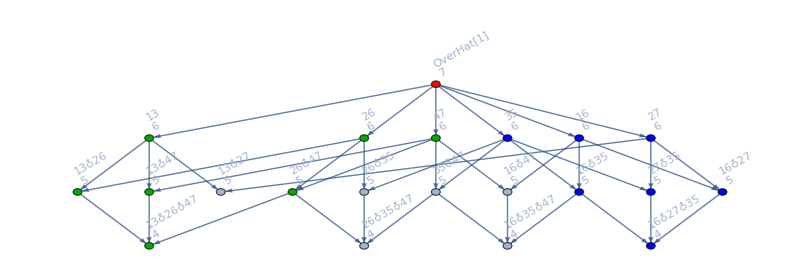

```mathematica
Graph[FormulaGraphReverse2[GAll[{1,3}]],VertexStyle->ColorSchemeForLists[g1,g3],ImageSize->800]
```

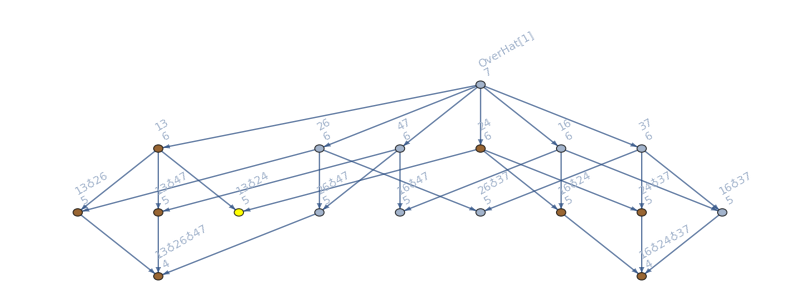

```mathematica
With[{formula=GAll[{1,2}]},
Graph[FormulaGraphReverse2[formula],VertexStyle->Join[
Map[#->Yellow&,Select[formula,With[{sets=SymbolToSets[#]},
HasTrianglePattern[sets]]&]],
Map[#->Brown&,Select[formula,With[{sets=SymbolToSets[#]},
Length[sets]≥4&&HasQuadrilateralPattern[sets]]&]]
],ImageSize->800]
]
```

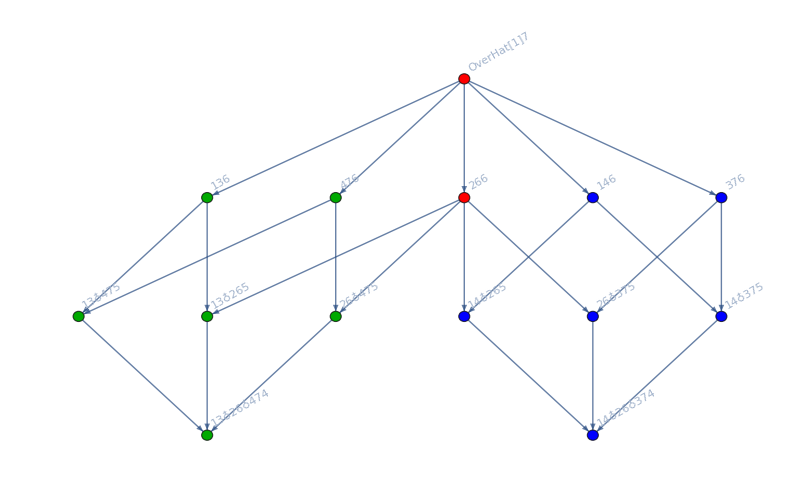

```mathematica
Graph[FormulaGraphReverse2[GAll[{1,4}]],VertexStyle->ColorSchemeForLists[g1,g4],ImageSize->800]
```

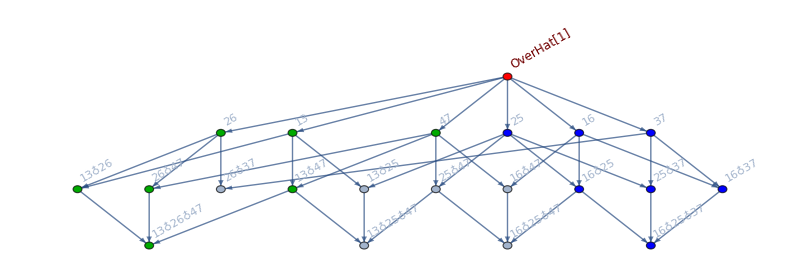

```mathematica
Graph[FormulaGraphReverse2[GAll[{1,5}]],VertexStyle->ColorSchemeForLists[g1,g5],ImageSize->800]
```

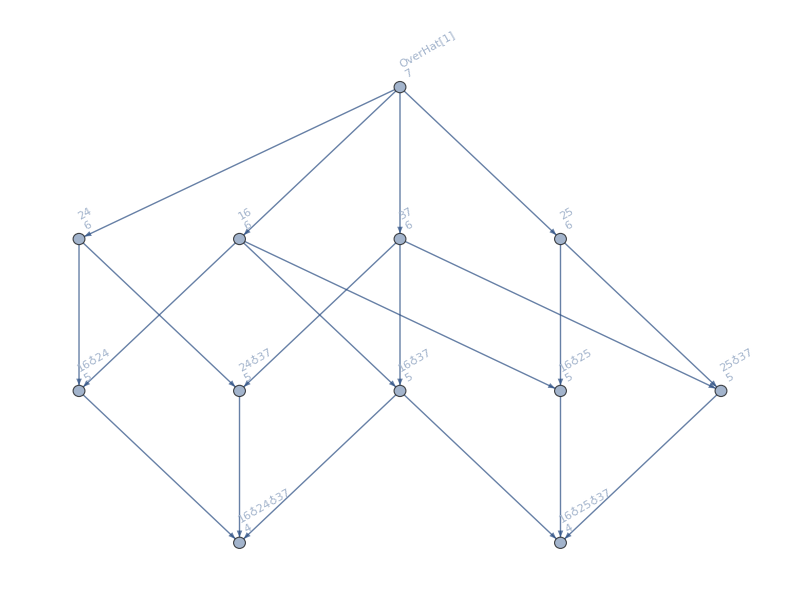
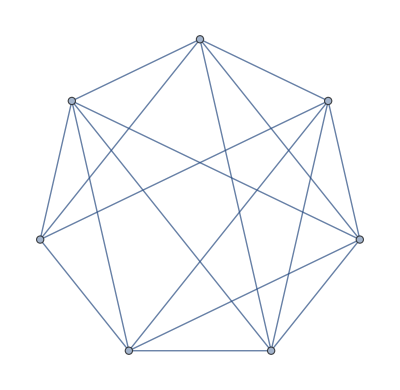

```mathematica
Labeled[Graph[FormulaGraphReverse2[GAll[{2,5}]],VertexStyle->ColorSchemeForLists[g2,g5],ImageSize->800],Graph[GAllGraph[{2,5}]]]
```

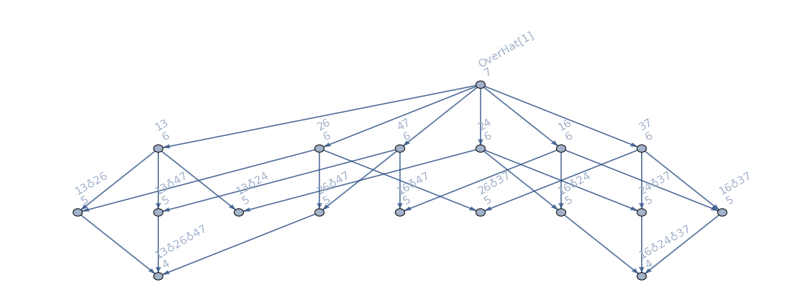
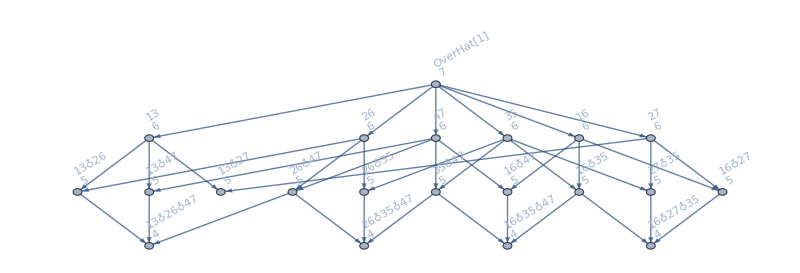
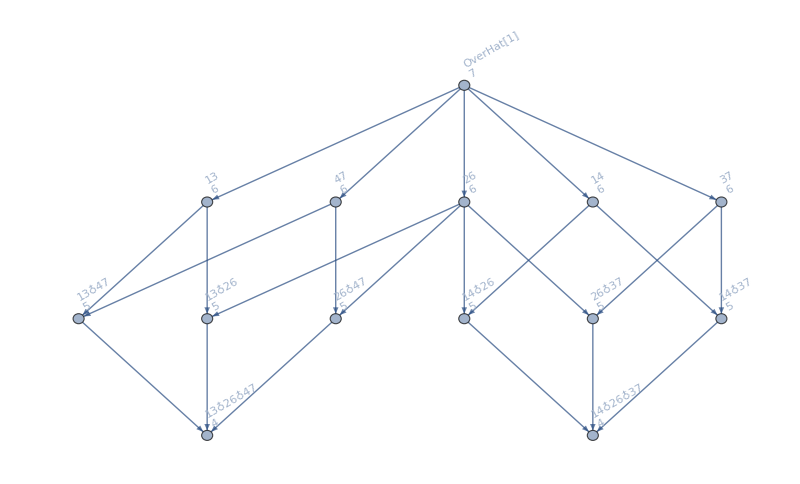
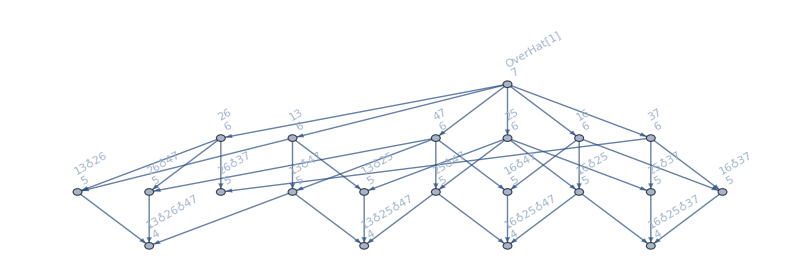
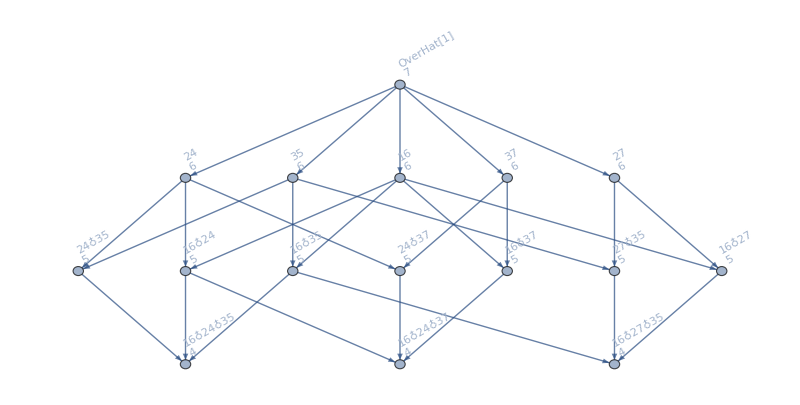
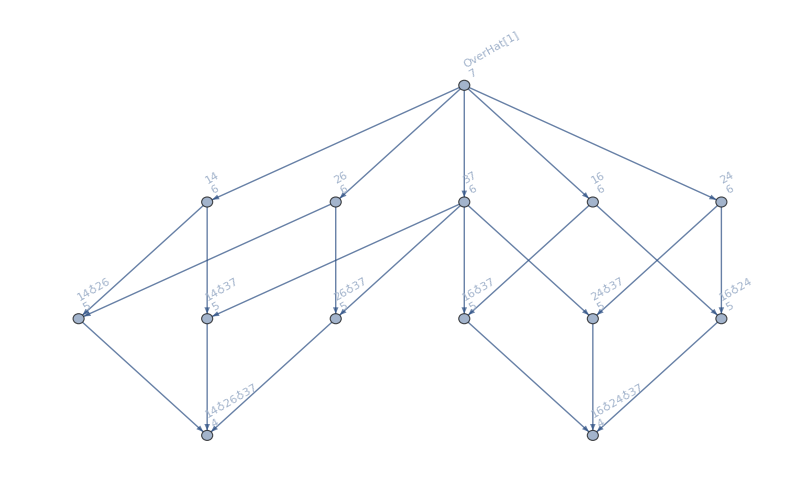
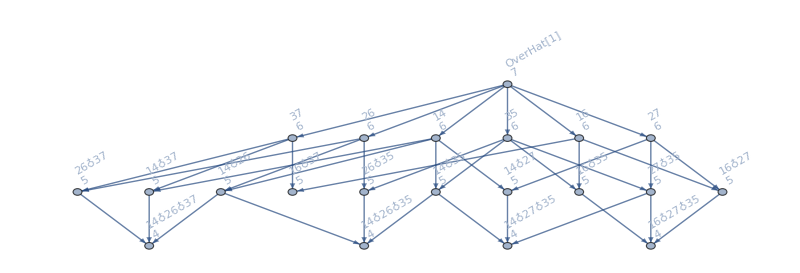
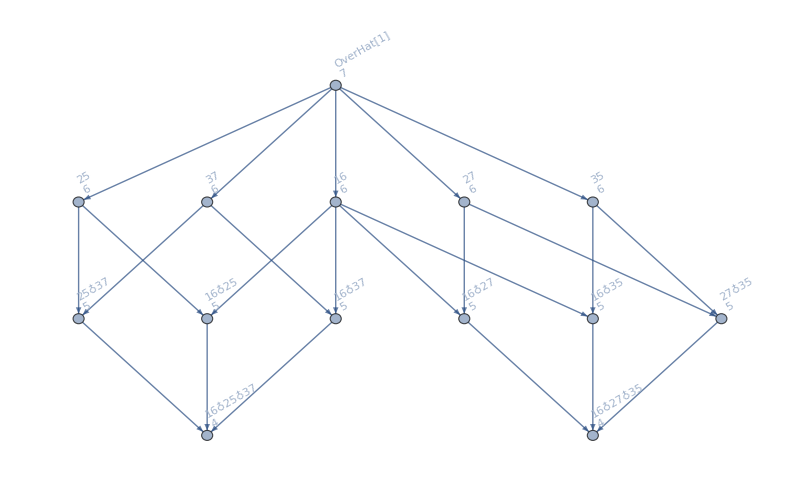
{-Graphics-{1,2},-Graphics-{1,3},-Graphics-{1,4},-Graphics-{1,5},-Graphics-{2,3},-Graphics-{2,4},-Graphics-{2,5},-Graphics-{3,4},-Graphics-{3,5},-Graphics-{4,5}}

```mathematica
Table[
With[{
first={g1,g2,g3,g4,g5}[[s[[1]]]],
second={g1,g2,g3,g4,g5}[[s[[2]]]]
},
With  [{formula=GAll[s]},
Labeled[
Graph[FormulaGraphReverse2[formula],VertexStyle->Join[
Map[#->Yellow&,Select[formula,With[{sets=SymbolToSets[#]},
HasTrianglePattern[sets]&&Length[sets]==4]&]],
Map[#->Brown&,Select[formula,With[{sets=SymbolToSets[#]},
HasQuadrilateralPattern[sets]&&Length[sets]==4]&]],
ColorSchemeForLists[first,second]
],ImageSize->800],
s]
]
],{s,Subsets[Range[5],{2}]}]
```

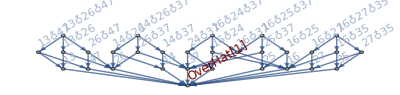

```mathematica
FormulaGraphReverse[DeleteDuplicates[Join[g1,g2,g3,g4,g5]]]
```

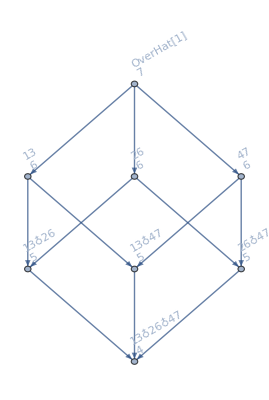
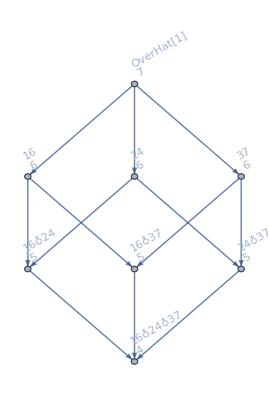
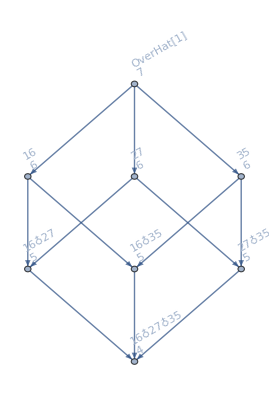
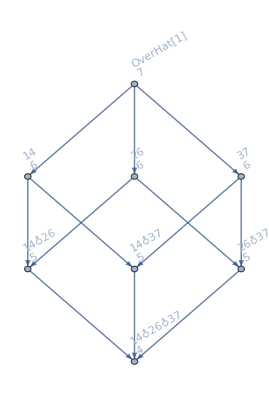
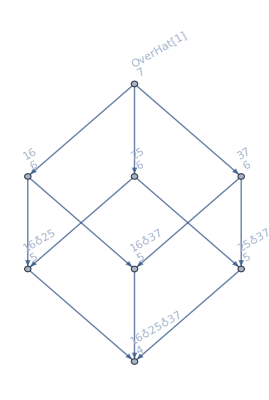

```mathematica
Table[
FormulaGraphReverse2[g],
{g,{g1,g2,g3,g4,g5}}
]
```

```mathematica
Map[Length,PartitionsWithLessBlocks[{{1,3},{2,6},{4,7},{5}}]]
```

{3,3,3,3,3,3}

```mathematica
Map[Length,PartitionsWithMoreBlocks[{{1,3},{2,6},{4,7},{5}}]]
```

{5,5,5}

```mathematica
Sort[Tally[Flatten[Map[PartitionsWithLessBlocks[ SymbolToSets[#]]&,g1],1]],#1[[2]]>#2[[2]]&]
```

{{{{1,3},{2,6},{4,7},{5}},3},{{{1,3},{2,6},{4},{5},{7}},2},{{{1},{2,6},{3},{4,7},{5}},2},{{{1,3},{2},{4,7},{5},{6}},2},{{{1,3},{2,6},{4,5,7}},1},{{{1,3},{2,5,6},{4,7}},1},{{{1,3},{2,4,6,7},{5}},1},{{{1,3,5},{2,6},{4,7}},1},{{{1,3,4,7},{2,6},{5}},1},{{{1,2,3,6},{4,7},{5}},1},{{{1,3},{2,6},{4},{5,7}},1},{{{1,3},{2,6},{4,5},{7}},1},{{{1,3},{2,6,7},{4},{5}},1},{{{1,3},{2,5,6},{4},{7}},1},{{{1,3},{2,4,6},{5},{7}},1},{{{1,3,7},{2,6},{4},{5}},1},{{{1,3,5},{2,6},{4},{7}},1},{{{1,3,4},{2,6},{5},{7}},1},{{{1,2,3,6},{4},{5},{7}},1},{{{1,3},{2},{4,7},{5,6}},1},{{{1,3},{2},{4,6,7},{5}},1},{{{1,3},{2},{4,5,7},{6}},1},{{{1,3},{2,5},{4,7},{6}},1},{{{1,3},{2,4,7},{5},{6}},1},{{{1,3,6},{2},{4,7},{5}},1},{{{1,3,5},{2},{4,7},{6}},1},{{{1,3,4,7},{2},{5},{6}},1},{{{1,2,3},{4,7},{5},{6}},1},{{{1,3},{2},{4},{5},{6,7}},1},{{{1,3},{2},{4},{5,7},{6}},1},{{{1,3},{2},{4},{5,6},{7}},1},{{{1,3},{2},{4,6},{5},{7}},1},{{{1,3},{2},{4,5},{6},{7}},1},{{{1,3},{2,7},{4},{5},{6}},1},{{{1,3},{2,5},{4},{6},{7}},1},{{{1,3},{2,4},{5},{6},{7}},1},{{{1,3,7},{2},{4},{5},{6}},1},{{{1,3,6},{2},{4},{5},{7}},1},{{{1,3,5},{2},{4},{6},{7}},1},{{{1,3,4},{2},{5},{6},{7}},1},{{{1,2,3},{4},{5},{6},{7}},1},{{{1},{2,6},{3},{4,5,7}},1},{{{1},{2,6},{3,5},{4,7}},1},{{{1},{2,6},{3,4,7},{5}},1},{{{1},{2,5,6},{3},{4,7}},1},{{{1},{2,4,6,7},{3},{5}},1},{{{1},{2,3,6},{4,7},{5}},1},{{{1,5},{2,6},{3},{4,7}},1},{{{1,4,7},{2,6},{3},{5}},1},{{{1,2,6},{3},{4,7},{5}},1},{{{1},{2,6},{3},{4},{5,7}},1},{{{1},{2,6},{3},{4,5},{7}},1},{{{1},{2,6},{3,7},{4},{5}},1},{{{1},{2,6},{3,5},{4},{7}},1},{{{1},{2,6},{3,4},{5},{7}},1},{{{1},{2,6,7},{3},{4},{5}},1},{{{1},{2,5,6},{3},{4},{7}},1},{{{1},{2,4,6},{3},{5},{7}},1},{{{1},{2,3,6},{4},{5},{7}},1},{{{1,7},{2,6},{3},{4},{5}},1},{{{1,5},{2,6},{3},{4},{7}},1},{{{1,4},{2,6},{3},{5},{7}},1},{{{1,2,6},{3},{4},{5},{7}},1},{{{1},{2},{3},{4,7},{5,6}},1},{{{1},{2},{3},{4,6,7},{5}},1},{{{1},{2},{3},{4,5,7},{6}},1},{{{1},{2},{3,6},{4,7},{5}},1},{{{1},{2},{3,5},{4,7},{6}},1},{{{1},{2},{3,4,7},{5},{6}},1},{{{1},{2,5},{3},{4,7},{6}},1},{{{1},{2,4,7},{3},{5},{6}},1},{{{1},{2,3},{4,7},{5},{6}},1},{{{1,6},{2},{3},{4,7},{5}},1},{{{1,5},{2},{3},{4,7},{6}},1},{{{1,4,7},{2},{3},{5},{6}},1},{{{1,2},{3},{4,7},{5},{6}},1},{{{1},{2},{3},{4},{5},{6,7}},1},{{{1},{2},{3},{4},{5,7},{6}},1},{{{1},{2},{3},{4},{5,6},{7}},1},{{{1},{2},{3},{4,7},{5},{6}},1},{{{1},{2},{3},{4,6},{5},{7}},1},{{{1},{2},{3},{4,5},{6},{7}},1},{{{1},{2},{3,7},{4},{5},{6}},1},{{{1},{2},{3,6},{4},{5},{7}},1},{{{1},{2},{3,5},{4},{6},{7}},1},{{{1},{2},{3,4},{5},{6},{7}},1},{{{1},{2,7},{3},{4},{5},{6}},1},{{{1},{2,6},{3},{4},{5},{7}},1},{{{1},{2,5},{3},{4},{6},{7}},1},{{{1},{2,4},{3},{5},{6},{7}},1},{{{1},{2,3},{4},{5},{6},{7}},1},{{{1,7},{2},{3},{4},{5},{6}},1},{{{1,6},{2},{3},{4},{5},{7}},1},{{{1,5},{2},{3},{4},{6},{7}},1},{{{1,4},{2},{3},{5},{6},{7}},1},{{{1,3},{2},{4},{5},{6},{7}},1},{{{1,2},{3},{4},{5},{6},{7}},1}}

```mathematica
Flatten[
Table[
Table[
Table[
Table[
Table[
With[{g=EdgeDelete[
CompleteGraph[7],
DeleteDuplicates[
Join[
EdgeList[GraphComplement[GraphFromSets[part1]]],
EdgeList[GraphComplement[GraphFromSets[part2]]],
EdgeList[GraphComplement[GraphFromSets[part3]]],
EdgeList[GraphComplement[GraphFromSets[part4]]],
EdgeList[GraphComplement[GraphFromSets[part5]]]
]
]
]},
With[{rep3=Join[
Map[#->Style[#,Red]&,Select[
FindFullFormula[g],
SymbolRank[#]==4&&!MemberQ[{SetsToSymbol[part1],SetsToSymbol[part5],SetsToSymbol[part2],SetsToSymbol[part3],SetsToSymbol[part4]},#]&]
],
Table[k->Style[k,Darker[Green]],{k,{SetsToSymbol[part1],SetsToSymbol[part5],SetsToSymbol[part2],SetsToSymbol[part3],SetsToSymbol[part4]}}]
]},
rep3
]
],
{part5,Take[QuadrilateralsWithPattern[7,5],1]}
],
{part4,Take[QuadrilateralsWithPattern[7,4],1]}
],
{part3,Take[QuadrilateralsWithPattern[7,3],1]}
],
{part2,Take[QuadrilateralsWithPattern[7,2],1]}
],
{part1,Take[QuadrilateralsWithPattern[7,1],1]}
],5]
```

{v13x26x47x5→v13x26x47x5,v16x25x37x4→v16x25x37x4,v16x24x37x5→v16x24x37x5,v16x27x35x4→v16x27x35x4,v14x26x37x5→v14x26x37x5}

```mathematica
With[
{},
Map[{SetsToSymbol[#[[1]]],#[[2]],Length[PartitionsWithMoreBlocksRecursive[#[[1]]]]}&,
Sort[Tally[Flatten[Map[PartitionsWithLessBlocksRecursive[ SymbolToSets[#]]&,
Join[g1,g2,g3,g4,g5]
],1]],#1[[2]]>#2[[2]]&]
]
]/.{v1x26x35x47->v1x26x35x47,v1x247x35x6->v1x247x35x6,v16x2x35x47->v16x2x35x47,v16x25x3x47->v16x25x3x47,v16x247x3x5->v16x247x3x5,v16x24x35x7->v16x24x35x7,v14x27x35x6->v14x27x35x6,v14x26x35x7->v14x26x35x7,v14x25x37x6->v14x25x37x6,v13x25x47x6->v13x25x47x6,v13x247x5x6->v13x247x5x6,v13x26x47x5->v13x26x47x5,v16x25x37x4->v16x25x37x4,v16x24x37x5->v16x24x37x5,v16x27x35x4->v16x27x35x4,v14x26x37x5->v14x26x37x5}
```

{{v1234567,40,876},{v123467x5,32,202},{v16x23457,28,103},{v12456x37,28,103},{v123567x4,28,202},{v1246x357,26,74},{v146x2357,25,74},{v1246x37x5,24,29},{v1347x256,23,74},{v16x2357x4,23,29},{v1367x245,22,74},{v13467x25,22,103},{v13457x26,22,103},{v1256x347,22,74},{v12467x35,22,103},{v16x245x37,21,19},{v1347x26x5,21,29},{v1x234567,20,202},{v156x2347,20,74},{v14x23567,20,103},{v13567x24,20,103},{v134567x2,20,202},{v126x3457,20,74},{v124567x3,20,202},{v12367x45,20,103},{v12356x47,20,103},{v123457x6,20,202},{v123456x7,20,202},{v16x2347x5,20,29},{v1256x37x4,20,29},{v12367x4x5,20,51},{v1356x247,19,74},{v16x24x357,19,19},{v146x25x37,19,19},{v16x25x347,18,19},{v1367x25x4,18,29},{v1367x24x5,18,29},{v13467x2x5,18,51},{v126x357x4,18,24},{v126x347x5,18,24},{v12467x3x5,18,51},{v1456x237,17,74},{v137x2456,17,74},{v136x2457,17,74},{v135x2467,17,74},{v16x247x35,17,19},{v156x24x37,17,19},{v14x256x37,17,19},{v146x2x357,17,24},{v146x237x5,17,24},{v15x23467,16,103},{v145x2367,16,74},{v13x24567,16,103},{v1357x246,16,74},{v13456x27,16,103},{v1267x345,16,74},{v1236x457,16,74},{v12347x56,16,103},{v12346x57,16,103},{v1x23567x4,16,51},{v1x23467x5,16,51},{v1x23457x6,16,51},{v16x2x3457,16,29},{v14x26x357,16,19},{v14x2367x5,16,29},{v13567x2x4,16,51},{v126x37x45,16,19},{v1267x35x4,16,29},{v1246x35x7,16,29},{v12456x3x7,16,51},{v1236x47x5,16,29},{v12356x4x7,16,51},{v12347x5x6,16,51},{v12346x5x7,16,51},{v16x25x37x4,16,7},{v16x24x37x5,16,7},{v126x37x4x5,16,9},{v1x256x347,15,24},{v1x2456x37,15,29},{v16x2457x3,15,29},{v16x237x45,15,19},{v156x237x4,15,24},{v14x2357x6,15,29},{v146x27x35,15,19},{v145x26x37,15,19},{v1456x2x37,15,29},{v13x2467x5,15,29},{v137x256x4,15,24},{v137x246x5,15,24},{v136x247x5,15,24},{v1356x27x4,15,29},{v1347x25x6,15,29},{v16x2x357x4,15,9},{v16x237x4x5,15,9},{v146x2x37x5,15,9},{v167x2345,14,74},{v1467x235,14,74},{v1346x257,14,74},{v1345x267,14,74},{v12567x34,14,103},{v1245x367,14,74},{v12357x46,14,103},{v1x26x3457,14,29},{v1x246x357,14,24},{v16x27x345,14,19},{v16x2345x7,14,29},{v156x2x347,14,24},{v13x256x47,14,19},{v1367x2x45,14,29},{v135x26x47,14,19},{v1357x26x4,14,29},{v13457x2x6,14,51},{v126x35x47,14,19},{v1256x3x47,14,29},{v12567x3x4,14,51},{v1246x3x57,14,29},{v1245x37x6,14,29},{v12357x4x6,14,51},{v16x2x347x5,14,9},{v14x26x37x5,14,7},{v1367x2x4x5,14,14},{v1246x3x5x7,14,14},{v147x2356,13,74},{v134x2567,13,74},{v124x3567,13,74},{v1x2467x35,13,29},{v1x2357x46,13,29},{v16x235x47,13,19},{v15x26x347,13,19},{v15x246x37,13,19},{v156x247x3,13,24},{v146x257x3,13,24},{v146x235x7,13,24},{v13x26x457,13,19},{v137x26x45,13,19},{v137x245x6,13,24},{v136x25x47,13,19},{v136x257x4,13,24},{v136x245x7,13,24},{v1356x2x47,13,29},{v1356x24x7,13,29},{v1347x2x56,13,29},{v124x357x6,13,24},{v1x26x347x5,13,9},{v1x256x37x4,13,9},{v1x246x37x5,13,9},{v1x2357x4x6,13,14},{v16x2x37x45,13,7},{v16x27x35x4,13,7},{v16x247x3x5,13,9},{v156x2x37x4,13,9},{v137x26x4x5,13,9},{v1347x2x5x6,13,14},{v1x245x367,12,24},{v1x24567x3,12,51},{v1x2367x45,12,29},{v1x2347x56,12,29},{v16x257x34,12,19},{v167x24x35,12,19},{v167x245x3,12,24},{v167x235x4,12,24},{v15x2367x4,12,29},{v15x2347x6,12,29},{v14x267x35,12,19},{v14x25x367,12,19},{v147x26x35,12,19},{v147x256x3,12,24},{v1467x2x35,12,29},{v1467x25x3,12,29},{v135x267x4,12,24},{v135x247x6,12,24},{v1357x24x6,12,29},{v134x267x5,12,24},{v134x256x7,12,24},{v1346x27x5,12,29},{v1346x25x7,12,29},{v1345x26x7,12,29},{v13456x2x7,12,51},{v126x3x457,12,24},{v126x345x7,12,24},{v1267x3x45,12,29},{v1267x34x5,12,29},{v1256x34x7,12,29},{v124x37x56,12,19},{v124x367x5,12,24},{v1236x4x57,12,29},{v1236x45x7,12,29},{v1x26x357x4,12,9},{v1x245x37x6,12,9},{v1x2367x4x5,12,14},{v1x2347x5x6,12,14},{v16x257x3x4,12,9},{v16x24x35x7,12,7},{v16x245x3x7,12,9},{v16x235x4x7,12,9},{v14x25x37x6,12,7},{v13x26x47x5,12,7},{v126x3x47x5,12,9},{v126x35x4x7,12,9},{v1267x3x4x5,12,14},{v1256x3x4x7,12,14},{v124x37x5x6,12,9},{v1236x4x5x7,12,14},{v1457x236,11,74},{v125x3467,11,74},{v1247x356,11,74},{v1x25x3467,11,29},{v1x24x3567,11,29},{v1x2356x47,11,29},{v15x2467x3,11,29},{v14x2x3567,11,29},{v14x2567x3,11,29},{v14x237x56,11,19},{v14x2356x7,11,29},{v147x236x5,11,24},{v145x237x6,11,24},{v1457x26x3,11,29},{v1456x27x3,11,29},{v13x2567x4,11,29},{v13x2457x6,11,29},{v13x2456x7,11,29},{v137x25x46,11,19},{v137x24x56,11,19},{v136x2x457,11,24},{v136x27x45,11,19},{v136x24x57,11,19},{v135x246x7,11,24},{v134x26x57,11,19},{v125x347x6,11,24},{v1247x35x6,11,29},{v1x26x37x45,11,7},{v1x25x347x6,11,9},{v1x24x357x6,11,9},{v1x2467x3x5,11,14},{v16x2x35x47,11,7},{v16x25x3x47,11,7},{v15x26x37x4,11,7},{v14x2x357x6,11,9},{v14x237x5x6,11,9},{v147x26x3x5,11,9},{v146x2x35x7,11,9},{v146x27x3x5,11,9},{v146x25x3x7,11,9},{v137x25x4x6,11,9},{v137x24x5x6,11,9},{v136x2x47x5,11,9},{v136x27x4x5,11,9},{v136x25x4x7,11,9},{v136x24x5x7,11,9},{v1356x2x4x7,11,14},{v134x26x5x7,11,9},{v16x2x37x4x5,11,3},{v17x23456,10,103},{v1567x234,10,74},{v14567x23,10,103},{v12x34567,10,103},{v12457x36,10,103},{v1237x456,10,74},{v1235x467,10,74},{v12345x67,10,103},{v1x2x34567,10,51},{v1x267x345,10,24},{v1x247x356,10,24},{v1x23456x7,10,51},{v16x234x57,10,19},{v167x2x345,10,24},{v167x25x34,10,19},{v167x234x5,10,24},{v15x24x367,10,19},{v156x27x34,10,19},{v156x234x7,10,24},{v1567x24x3,10,29},{v1467x23x5,10,29},{v145x2x367,10,24},{v145x267x3,10,24},{v14567x2x3,10,51},{v13x267x45,10,19},{v13x247x56,10,19},{v13x246x57,10,19},{v1357x2x46,10,29},{v1346x2x57,10,29},{v1345x27x6,10,29},{v12x3457x6,10,29},{v126x34x57,10,19},{v125x37x46,10,19},{v125x367x4,10,24},{v12457x3x6,10,51},{v1237x4x56,10,29},{v1237x46x5,10,29},{v1237x45x6,10,29},{v1235x47x6,10,29},{v12345x6x7,10,51},{v1x2x3457x6,10,14},{v1x26x35x47,10,7},{v1x267x35x4,10,9},{v1x25x37x46,10,7},{v1x25x367x4,10,9},{v1x256x3x47,10,9},{v1x24x37x56,10,7},{v1x24x367x5,10,9},{v1x247x35x6,10,9},{v16x2x345x7,10,9},{v16x27x3x45,10,7},{v16x27x34x5,10,7},{v16x25x34x7,10,7},{v16x24x3x57,10,7},{v16x234x5x7,10,9},{v167x2x35x4,10,9},{v167x25x3x4,10,9},{v167x24x3x5,10,9},{v15x24x37x6,10,7},{v156x27x3x4,10,9},{v156x24x3x7,10,9},{v14x2x37x56,10,7},{v14x2x367x5,10,9},{v14x26x35x7,10,7},{v14x267x3x5,10,9},{v14x256x3x7,10,9},{v1467x2x3x5,10,14},{v145x2x37x6,10,9},{v13x267x4x5,10,9},{v13x256x4x7,10,9},{v13x247x5x6,10,9},{v13x246x5x7,10,9},{v135x26x4x7,10,9},{v1357x2x4x6,10,14},{v1346x2x5x7,10,14},{v126x3x4x57,10,9},{v126x3x45x7,10,9},{v126x34x5x7,10,9},{v125x37x4x6,10,9},{v1237x4x5x6,10,14},{v1x26x37x4x5,10,3},{v126x3x4x5x7,10,4},{v1x2567x34,9,29},{v1x2457x36,9,29},{v1x237x456,9,24},{v1x236x457,9,24},{v17x246x35,9,19},{v17x2456x3,9,29},{v17x2356x4,9,29},{v16x23x457,9,19},{v15x2x3467,9,29},{v15x237x46,9,19},{v15x236x47,9,19},{v156x23x47,9,19},{v14x27x356,9,19},{v14x236x57,9,19},{v147x235x6,9,24},{v146x23x57,9,19},{v145x236x7,9,24},{v1456x23x7,9,29},{v13x25x467,9,19},{v137x2x456,9,24},{v135x2x467,9,24},{v135x27x46,9,19},{v134x257x6,9,24},{v12x357x46,9,19},{v12x3567x4,9,29},{v12x347x56,9,19},{v12x3467x5,9,29},{v1247x3x56,9,29},{v1247x36x5,9,29},{v1x2x357x46,9,9},{v1x2x3567x4,9,14},{v1x2x347x56,9,9},{v1x2x3467x5,9,14},{v1x26x3x457,9,9},{v1x2567x3x4,9,14},{v1x246x35x7,9,9},{v1x2457x3x6,9,14},{v1x2456x3x7,9,14},{v1x237x4x56,9,9},{v1x237x46x5,9,9},{v1x237x45x6,9,9},{v1x236x47x5,9,9},{v1x2356x4x7,9,14},{v16x2x3x457,9,9},{v16x23x47x5,9,7},{v15x2x347x6,9,9},{v15x26x3x47,9,7},{v15x237x4x6,9,9},{v156x2x3x47,9,9},{v14x27x35x6,9,7},{v14x26x3x57,9,7},{v14x236x5x7,9,9},{v146x2x3x57,9,9},{v146x23x5x7,9,9},{v145x26x3x7,9,9},{v1456x2x3x7,9,14},{v13x26x4x57,9,7},{v13x26x45x7,9,7},{v13x25x47x6,9,7},{v137x2x4x56,9,9},{v137x2x46x5,9,9},{v137x2x45x6,9,9},{v136x2x4x57,9,9},{v136x2x45x7,9,9},{v135x2x47x6,9,9},{v135x27x4x6,9,9},{v12x357x4x6,9,9},{v12x347x5x6,9,9},{v1247x3x5x6,9,14},{v1x2x357x4x6,9,4},{v1x2x347x5x6,9,4},{v1x25x37x4x6,9,3},{v1x24x37x5x6,9,3},{v1x237x4x5x6,9,4},{v16x2x3x47x5,9,3},{v16x2x35x4x7,9,3},{v16x27x3x4x5,9,3},{v16x25x3x4x7,9,3},{v16x24x3x5x7,9,3},{v14x2x37x5x6,9,3},{v146x2x3x5x7,9,4},{v137x2x4x5x6,9,4},{v136x2x4x5x7,9,4},{v157x2346,8,74},{v127x3456,8,74},{v123x4567,8,74},{v1234x567,8,74},{v1x27x3456,8,29},{v1x235x467,8,24},{v1x2346x57,8,29},{v1x2345x67,8,29},{v17x26x345,8,19},{v17x256x34,8,19},{v17x2346x5,8,29},{v17x2345x6,8,29},{v167x23x45,8,19},{v15x267x34,8,19},{v15x247x36,8,19},{v15x2346x7,8,29},{v157x246x3,8,24},{v1567x2x34,8,29},{v1567x23x4,8,29},{v14x257x36,8,19},{v14x235x67,8,19},{v147x2x356,8,24},{v147x25x36,8,19},{v13x2x4567,8,29},{v13x257x46,8,19},{v13x245x67,8,19},{v135x24x67,8,19},{v134x27x56,8,19},{v134x25x67,8,19},{v1345x2x67,8,29},{v12x37x456,8,19},{v12x367x45,8,19},{v127x35x46,8,19},{v127x356x4,8,24},{v127x345x6,8,24},{v124x35x67,8,19},{v124x356x7,8,24},{v1245x3x67,8,29},{v1245x36x7,8,29},{v123x47x56,8,19},{v123x467x5,8,24},{v123x457x6,8,24},{v1235x4x67,8,29},{v1235x46x7,8,29},{v1234x5x67,8,29},{v1234x57x6,8,29},{v1234x56x7,8,29},{v1x2x37x456,8,9},{v1x2x367x45,8,9},{v1x27x35x46,8,7},{v1x27x356x4,8,9},{v1x27x345x6,8,9},{v1x26x345x7,8,9},{v1x267x3x45,8,9},{v1x267x34x5,8,9},{v1x256x34x7,8,9},{v1x247x3x56,8,9},{v1x247x36x5,8,9},{v1x246x3x57,8,9},{v1x235x47x6,8,9},{v1x2346x5x7,8,14},{v1x2345x6x7,8,14},{v17x26x35x4,8,7},{v17x256x3x4,8,9},{v17x246x3x5,8,9},{v16x2x34x57,8,7},{v16x23x4x57,8,7},{v16x23x45x7,8,7},{v167x2x3x45,8,9},{v167x2x34x5,8,9},{v167x23x4x5,8,9},{v15x2x37x46,8,7},{v15x2x367x4,8,9},{v15x267x3x4,8,9},{v15x247x3x6,8,9},{v15x246x3x7,8,9},{v156x2x34x7,8,9},{v156x23x4x7,8,9},{v1567x2x3x4,8,14},{v14x257x3x6,8,9},{v14x235x6x7,8,9},{v147x2x35x6,8,9},{v147x25x3x6,8,9},{v13x2x47x56,8,7},{v13x2x467x5,8,9},{v13x2x457x6,8,9},{v13x257x4x6,8,9},{v13x245x6x7,8,9},{v135x24x6x7,8,9},{v134x27x5x6,8,9},{v134x25x6x7,8,9},{v1345x2x6x7,8,14},{v12x37x4x56,8,7},{v12x37x46x5,8,7},{v12x37x45x6,8,7},{v12x367x4x5,8,9},{v127x35x4x6,8,9},{v124x35x6x7,8,9},{v1245x3x6x7,8,14},{v123x47x5x6,8,9},{v1235x4x6x7,8,14},{v1234x5x6x7,8,14},{v1x2x37x4x56,8,3},{v1x2x37x46x5,8,3},{v1x2x37x45x6,8,3},{v1x2x367x4x5,8,4},{v1x26x3x47x5,8,3},{v1x26x35x4x7,8,3},{v1x267x3x4x5,8,4},{v1x256x3x4x7,8,4},{v1x247x3x5x6,8,4},{v1x246x3x5x7,8,4},{v16x2x3x4x57,8,3},{v16x2x3x45x7,8,3},{v16x2x34x5x7,8,3},{v16x23x4x5x7,8,3},{v167x2x3x4x5,8,4},{v15x2x37x4x6,8,3},{v156x2x3x4x7,8,4},{v14x26x3x5x7,8,3},{v13x26x4x5x7,8,3},{v12x37x4x5x6,8,3},{v1257x346,7,74},{v1x257x346,7,24},{v17x24x356,7,19},{v17x245x36,7,19},{v17x236x45,7,19},{v17x235x46,7,19},{v157x26x34,7,19},{v157x236x4,7,24},{v147x23x56,7,19},{v145x27x36,7,19},{v1457x2x36,7,29},{v1457x23x6,7,29},{v13x27x456,7,19},{v13x24x567,7,19},{v134x2x567,7,24},{v12x35x467,7,19},{v12x356x47,7,19},{v125x3x467,7,24},{v125x36x47,7,19},{v1257x3x46,7,29},{v1257x36x4,7,29},{v1257x34x6,7,29},{v124x3x567,7,24},{v124x36x57,7,19},{v1x2x35x467,7,9},{v1x2x356x47,7,9},{v1x26x34x57,7,7},{v1x25x3x467,7,9},{v1x25x36x47,7,7},{v1x257x3x46,7,9},{v1x257x36x4,7,9},{v1x257x34x6,7,9},{v1x24x35x67,7,7},{v1x24x356x7,7,9},{v1x245x3x67,7,9},{v1x245x36x7,7,9},{v1x236x4x57,7,9},{v1x236x45x7,7,9},{v1x235x4x67,7,9},{v1x235x46x7,7,9},{v17x26x3x45,7,7},{v17x26x34x5,7,7},{v17x24x35x6,7,7},{v17x245x3x6,7,9},{v17x236x4x5,7,9},{v17x235x4x6,7,9},{v15x26x34x7,7,7},{v15x236x4x7,7,9},{v157x26x3x4,7,9},{v14x2x35x67,7,7},{v14x2x356x7,7,9},{v14x27x3x56,7,7},{v14x27x36x5,7,7},{v14x25x3x67,7,7},{v14x25x36x7,7,7},{v147x2x3x56,7,9},{v147x2x36x5,7,9},{v147x23x5x6,7,9},{v145x27x3x6,7,9},{v1457x2x3x6,7,14},{v13x27x4x56,7,7},{v13x27x46x5,7,7},{v13x27x45x6,7,7},{v13x25x4x67,7,7},{v13x25x46x7,7,7},{v13x24x5x67,7,7},{v13x24x57x6,7,7},{v13x24x56x7,7,7},{v135x2x4x67,7,9},{v135x2x46x7,7,9},{v134x2x5x67,7,9},{v134x2x57x6,7,9},{v134x2x56x7,7,9},{v12x35x47x6,7,7},{v125x3x47x6,7,9},{v1257x3x4x6,7,14},{v124x3x5x67,7,9},{v124x3x57x6,7,9},{v124x3x56x7,7,9},{v124x36x5x7,7,9},{v1x2x35x47x6,7,3},{v1x27x35x4x6,7,3},{v1x26x3x4x57,7,3},{v1x26x3x45x7,7,3},{v1x26x34x5x7,7,3},{v1x25x3x47x6,7,3},{v1x257x3x4x6,7,4},{v1x24x35x6x7,7,3},{v1x245x3x6x7,7,4},{v1x236x4x5x7,7,4},{v1x235x4x6x7,7,4},{v17x26x3x4x5,7,3},{v15x26x3x4x7,7,3},{v14x2x35x6x7,7,3},{v14x27x3x5x6,7,3},{v14x25x3x6x7,7,3},{v147x2x3x5x6,7,4},{v13x2x47x5x6,7,3},{v13x27x4x5x6,7,3},{v13x25x4x6x7,7,3},{v13x24x5x6x7,7,3},{v135x2x4x6x7,7,4},{v134x2x5x6x7,7,4},{v124x3x5x6x7,7,4},{v1x23x4567,6,29},{v1x234x567,6,24},{v17x2x3456,6,29},{v17x25x346,6,19},{v17x234x56,6,19},{v15x27x346,6,19},{v15x23x467,6,19},{v15x234x67,6,19},{v157x24x36,6,19},{v157x234x6,6,24},{v14x23x567,6,19},{v145x23x67,6,19},{v12x3x4567,6,29},{v12x36x457,6,19},{v12x345x67,6,19},{v12x3456x7,6,29},{v127x3x456,6,24},{v127x36x45,6,19},{v127x34x56,6,19},{v127x346x5,6,24},{v125x34x67,6,19},{v125x346x7,6,24},{v123x4x567,6,24},{v123x46x57,6,19},{v123x45x67,6,19},{v123x456x7,6,24},{v1x2x3x4567,6,14},{v1x2x36x457,6,9},{v1x2x345x67,6,9},{v1x2x3456x7,6,14},{v1x27x3x456,6,9},{v1x27x36x45,6,7},{v1x27x34x56,6,7},{v1x27x346x5,6,9},{v1x25x34x67,6,7},{v1x25x346x7,6,9},{v1x24x3x567,6,9},{v1x24x36x57,6,7},{v1x23x47x56,6,7},{v1x23x467x5,6,9},{v1x23x457x6,6,9},{v1x234x5x67,6,9},{v1x234x57x6,6,9},{v1x234x56x7,6,9},{v17x2x35x46,6,7},{v17x2x356x4,6,9},{v17x2x345x6,6,9},{v17x25x3x46,6,7},{v17x25x36x4,6,7},{v17x25x34x6,6,7},{v17x24x3x56,6,7},{v17x24x36x5,6,7},{v17x234x5x6,6,9},{v15x2x3x467,6,9},{v15x2x36x47,6,7},{v15x27x3x46,6,7},{v15x27x36x4,6,7},{v15x27x34x6,6,7},{v15x24x3x67,6,7},{v15x24x36x7,6,7},{v15x23x47x6,6,7},{v15x234x6x7,6,9},{v157x24x3x6,6,9},{v14x2x3x567,6,9},{v14x2x36x57,6,7},{v14x23x5x67,6,7},{v14x23x57x6,6,7},{v14x23x56x7,6,7},{v145x2x3x67,6,9},{v145x2x36x7,6,9},{v145x23x6x7,6,9},{v13x2x4x567,6,9},{v13x2x46x57,6,7},{v13x2x45x67,6,7},{v13x2x456x7,6,9},{v12x3x47x56,6,7},{v12x3x467x5,6,9},{v12x3x457x6,6,9},{v12x36x47x5,6,7},{v12x35x4x67,6,7},{v12x35x46x7,6,7},{v12x356x4x7,6,9},{v12x345x6x7,6,9},{v127x3x4x56,6,9},{v127x3x46x5,6,9},{v127x3x45x6,6,9},{v127x36x4x5,6,9},{v127x34x5x6,6,9},{v125x3x4x67,6,9},{v125x3x46x7,6,9},{v125x36x4x7,6,9},{v125x34x6x7,6,9},{v123x4x5x67,6,9},{v123x4x57x6,6,9},{v123x4x56x7,6,9},{v123x46x5x7,6,9},{v123x45x6x7,6,9},{v1x2x3x47x56,6,3},{v1x2x3x467x5,6,4},{v1x2x3x457x6,6,4},{v1x2x36x47x5,6,3},{v1x2x35x4x67,6,3},{v1x2x35x46x7,6,3},{v1x2x356x4x7,6,4},{v1x2x345x6x7,6,4},{v1x27x3x4x56,6,3},{v1x27x3x46x5,6,3},{v1x27x3x45x6,6,3},{v1x27x36x4x5,6,3},{v1x27x34x5x6,6,3},{v1x25x3x4x67,6,3},{v1x25x3x46x7,6,3},{v1x25x36x4x7,6,3},{v1x25x34x6x7,6,3},{v1x24x3x5x67,6,3},{v1x24x3x57x6,6,3},{v1x24x3x56x7,6,3},{v1x24x36x5x7,6,3},{v1x23x47x5x6,6,3},{v1x234x5x6x7,6,4},{v17x2x35x4x6,6,3},{v17x25x3x4x6,6,3},{v17x24x3x5x6,6,3},{v15x2x3x47x6,6,3},{v15x27x3x4x6,6,3},{v15x24x3x6x7,6,3},{v14x2x3x5x67,6,3},{v14x2x3x57x6,6,3},{v14x2x3x56x7,6,3},{v14x2x36x5x7,6,3},{v14x23x5x6x7,6,3},{v145x2x3x6x7,6,4},{v13x2x4x5x67,6,3},{v13x2x4x57x6,6,3},{v13x2x4x56x7,6,3},{v13x2x46x5x7,6,3},{v13x2x45x6x7,6,3},{v12x3x47x5x6,6,3},{v12x35x4x6x7,6,3},{v127x3x4x5x6,6,4},{v125x3x4x6x7,6,4},{v123x4x5x6x7,6,4},{v17x23x456,5,19},{v157x2x346,5,24},{v157x23x46,5,19},{v12x34x567,5,19},{v12x346x57,5,19},{v1x2x34x567,5,9},{v1x2x346x57,5,9},{v1x23x4x567,5,9},{v1x23x46x57,5,7},{v1x23x45x67,5,7},{v1x23x456x7,5,9},{v17x2x3x456,5,9},{v17x2x36x45,5,7},{v17x2x34x56,5,7},{v17x2x346x5,5,9},{v17x23x4x56,5,7},{v17x23x46x5,5,7},{v17x23x45x6,5,7},{v15x2x34x67,5,7},{v15x2x346x7,5,9},{v15x23x4x67,5,7},{v15x23x46x7,5,7},{v157x2x3x46,5,9},{v157x2x36x4,5,9},{v157x2x34x6,5,9},{v157x23x4x6,5,9},{v12x3x4x567,5,9},{v12x3x46x57,5,7},{v12x3x45x67,5,7},{v12x3x456x7,5,9},{v12x36x4x57,5,7},{v12x36x45x7,5,7},{v12x34x5x67,5,7},{v12x34x57x6,5,7},{v12x34x56x7,5,7},{v12x346x5x7,5,9},{v1x2x3x4x567,5,4},{v1x2x3x46x57,5,3},{v1x2x3x45x67,5,3},{v1x2x3x456x7,5,4},{v1x2x36x4x57,5,3},{v1x2x36x45x7,5,3},{v1x2x34x5x67,5,3},{v1x2x34x57x6,5,3},{v1x2x34x56x7,5,3},{v1x2x346x5x7,5,4},{v1x23x4x5x67,5,3},{v1x23x4x57x6,5,3},{v1x23x4x56x7,5,3},{v1x23x46x5x7,5,3},{v1x23x45x6x7,5,3},{v17x2x3x4x56,5,3},{v17x2x3x46x5,5,3},{v17x2x3x45x6,5,3},{v17x2x36x4x5,5,3},{v17x2x34x5x6,5,3},{v17x23x4x5x6,5,3},{v15x2x3x4x67,5,3},{v15x2x3x46x7,5,3},{v15x2x36x4x7,5,3},{v15x2x34x6x7,5,3},{v15x23x4x6x7,5,3},{v157x2x3x4x6,5,4},{v12x3x4x5x67,5,3},{v12x3x4x57x6,5,3},{v12x3x4x56x7,5,3},{v12x3x46x5x7,5,3},{v12x3x45x6x7,5,3},{v12x36x4x5x7,5,3},{v12x34x5x6x7,5,3},{v1x2x3x4x5x67,5,1},{v1x2x3x4x57x6,5,1},{v1x2x3x4x56x7,5,1},{v1x2x3x47x5x6,5,1},{v1x2x3x46x5x7,5,1},{v1x2x3x45x6x7,5,1},{v1x2x37x4x5x6,5,1},{v1x2x36x4x5x7,5,1},{v1x2x35x4x6x7,5,1},{v1x2x34x5x6x7,5,1},{v1x27x3x4x5x6,5,1},{v1x26x3x4x5x7,5,1},{v1x25x3x4x6x7,5,1},{v1x24x3x5x6x7,5,1},{v1x23x4x5x6x7,5,1},{v17x2x3x4x5x6,5,1},{v16x2x3x4x5x7,5,1},{v15x2x3x4x6x7,5,1},{v14x2x3x5x6x7,5,1},{v13x2x4x5x6x7,5,1},{v12x3x4x5x6x7,5,1}}

```mathematica
Length[%]
```

876

```mathematica
Map[{SetsToLabel[#[[1]]],#[[2]]}&,Sort[Tally[Flatten[Map[PartitionsWithLessBlocks[ SymbolToSets[#]]&,g2],1]],#1[[2]]>#2[[2]]&]]
```

{{16♁24♁37♁5,3},{16♁24♁3♁5♁7,2},{1♁24♁37♁5♁6,2},{16♁2♁37♁4♁5,2},{16♁24♁357,1},{16♁245♁37,1},{16♁2347♁5,1},{156♁24♁37,1},{1367♁24♁5,1},{1246♁37♁5,1},{16♁24♁3♁57,1},{16♁24♁35♁7,1},{16♁247♁3♁5,1},{16♁245♁3♁7,1},{16♁234♁5♁7,1},{167♁24♁3♁5,1},{156♁24♁3♁7,1},{136♁24♁5♁7,1},{1246♁3♁5♁7,1},{16♁2♁37♁45,1},{16♁2♁357♁4,1},{16♁2♁347♁5,1},{16♁25♁37♁4,1},{16♁237♁4♁5,1},{156♁2♁37♁4,1},{146♁2♁37♁5,1},{1367♁2♁4♁5,1},{126♁37♁4♁5,1},{16♁2♁3♁4♁57,1},{16♁2♁3♁47♁5,1},{16♁2♁3♁45♁7,1},{16♁2♁35♁4♁7,1},{16♁2♁34♁5♁7,1},{16♁27♁3♁4♁5,1},{16♁25♁3♁4♁7,1},{16♁23♁4♁5♁7,1},{167♁2♁3♁4♁5,1},{156♁2♁3♁4♁7,1},{146♁2♁3♁5♁7,1},{136♁2♁4♁5♁7,1},{126♁3♁4♁5♁7,1},{1♁24♁37♁56,1},{1♁24♁367♁5,1},{1♁24♁357♁6,1},{1♁246♁37♁5,1},{1♁245♁37♁6,1},{1♁2347♁5♁6,1},{15♁24♁37♁6,1},{137♁24♁5♁6,1},{124♁37♁5♁6,1},{1♁24♁3♁5♁67,1},{1♁24♁3♁57♁6,1},{1♁24♁3♁56♁7,1},{1♁24♁36♁5♁7,1},{1♁24♁35♁6♁7,1},{1♁247♁3♁5♁6,1},{1♁246♁3♁5♁7,1},{1♁245♁3♁6♁7,1},{1♁234♁5♁6♁7,1},{17♁24♁3♁5♁6,1},{15♁24♁3♁6♁7,1},{13♁24♁5♁6♁7,1},{124♁3♁5♁6♁7,1},{1♁2♁37♁4♁56,1},{1♁2♁37♁46♁5,1},{1♁2♁37♁45♁6,1},{1♁2♁367♁4♁5,1},{1♁2♁357♁4♁6,1},{1♁2♁347♁5♁6,1},{1♁26♁37♁4♁5,1},{1♁25♁37♁4♁6,1},{1♁237♁4♁5♁6,1},{15♁2♁37♁4♁6,1},{14♁2♁37♁5♁6,1},{137♁2♁4♁5♁6,1},{12♁37♁4♁5♁6,1},{1♁2♁3♁4♁5♁67,1},{1♁2♁3♁4♁57♁6,1},{1♁2♁3♁4♁56♁7,1},{1♁2♁3♁47♁5♁6,1},{1♁2♁3♁46♁5♁7,1},{1♁2♁3♁45♁6♁7,1},{1♁2♁37♁4♁5♁6,1},{1♁2♁36♁4♁5♁7,1},{1♁2♁35♁4♁6♁7,1},{1♁2♁34♁5♁6♁7,1},{1♁27♁3♁4♁5♁6,1},{1♁26♁3♁4♁5♁7,1},{1♁25♁3♁4♁6♁7,1},{1♁24♁3♁5♁6♁7,1},{1♁23♁4♁5♁6♁7,1},{17♁2♁3♁4♁5♁6,1},{16♁2♁3♁4♁5♁7,1},{15♁2♁3♁4♁6♁7,1},{14♁2♁3♁5♁6♁7,1},{13♁2♁4♁5♁6♁7,1},{12♁3♁4♁5♁6♁7,1}}

```mathematica
2^30
```

1073741824

## Looking a fractions

```mathematica
(*Monitor[
Table[
With[{
first={g1,g2,g3,g4,g5}[[s[[1]]]],
second={g1,g2,g3,g4,g5}[[s[[2]]]]
},
Intersection[PartitionsWithMoreBlocksRecursive[Map[SymbolToSets, first]],PartitionsWithMoreBlocksRecursive[Map[SymbolToSets, second]]]
(*Labeled[
Graph[FormulaGraphReverse2[GAll[s]],VertexStyle->ColorSchemeForLists[first,second],ImageSize->800],
s]*)
],{s,RandomSample[Subsets[Range[5],{2}],1]}],
s]*)
```